```mathematica
Clear["Global`*"];
ω=2000 ;
c1[ζ_]:=-ζ ω + ω √(ζ^2-1);
c2[ζ_]:=-ζ ω - ω √(ζ^2-1);
H[ζ_]:=ω^2/((s-c1[ζ])(s-c2[ζ]));
```

```mathematica
StepR[t_,ζ_]:=ω^2/(c1[ζ]-c2[ζ])*((ⅇ^(c1[ζ]t)-1)/c1[ζ]-(ⅇ^(c2[ζ]t)-1)/c2[ζ]) (* Unit Impulse Integrated by hand -> Unit step Response *)
```

```mathematica
H1=ω^2/(s+ ω)^2 (* Transfer function when ζ=1 *)
(* Relevant Time Domain Function -> t*ⅇ^-ωt*u(t) StepR1 means the Integral of it as below *)
```

```mathematica
StepR1[t_]:=ω^2∫_0^t τ*Exp[-ω τ]*UnitStep[τ]ⅆτ
```

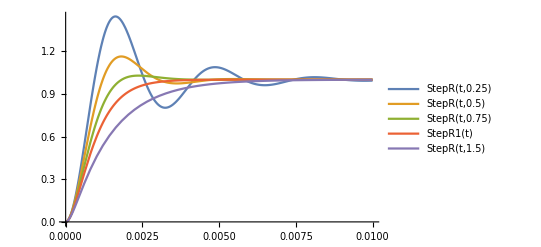

```mathematica
Plot[{StepR[t,0.25],StepR[t,0.5],StepR[t,0.75],StepR1[t],StepR[t,1.5]},{t,0,0.010},PlotRange->All,PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Control`PoleZeroPlot[{H[ζ]},PlotLabel->StringForm["Pole Zero Plot for ζ = `1`",ζ],PlotLegends->StringForm["ζ = `1` ",ζ],PoleZeroMarkers-> Style["x",Large,Background->Cyan],AxesLabel->{"Re","Im"}],{{ζ,0.5},0,1}]
```